```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
F1pQ4data:=ErrorListPlot[{{{0.156,0.016999937},ErrorBar[{-0.00022574,0.00022574}]},{{0.179,0.021156833},ErrorBar[{-0.000196706,0.000196706}]},{{0.195,0.02510612},ErrorBar[{-0.000327034,0.000327034}]},{{0.234,0.033193142},ErrorBar[{-0.000370685,0.000370685}]},{{0.273,0.041128754},ErrorBar[{-0.000385181,0.000385181}]},{{0.292,0.04572751},ErrorBar[{-0.000426474,0.000426474}]},{{0.312,0.050472767},ErrorBar[{-0.000470731,0.000470731}]},{{0.35,0.060173593},ErrorBar[{-0.00074212,0.00074212}]},{{0.389,0.070607438},ErrorBar[{-0.000574628,0.000574628}]},{{0.428,0.081773521},ErrorBar[{-0.000983249,0.000983249}]},{{0.467,0.091558778},ErrorBar[{-0.000829002,0.000829002}]},{{0.506,0.101076612},ErrorBar[{-0.001227652,0.001227652}]},{{0.545,0.112591782},ErrorBar[{-0.001012312,0.001012312}]},{{0.584,0.122974562},ErrorBar[{-0.001471281,0.001471281}]},{{0.623,0.132266212},ErrorBar[{-0.001061315,0.001061315}]},{{0.662,0.145057888},ErrorBar[{-0.001711601,0.001711601}]},{{0.701,0.153871904},ErrorBar[{-0.001372498,0.001372498}]},{{0.74,0.168579755},ErrorBar[{-0.001947025,0.001947025}]},{{0.779,0.175835821},ErrorBar[{-0.001546941,0.001546941}]},{{0.857,0.203723667},ErrorBar[{-0.002098277,0.002098277}]},{{0.389,0.070822919},ErrorBar[{-0.0015084,0.0015084}]},{{0.584,0.122852123},ErrorBar[{-0.002574744,0.002574744}]},{{0.779,0.174460719},ErrorBar[{-0.003609527,0.003609527}]},{{0.973,0.225425642},ErrorBar[{-0.004791661,0.004791661}]},{{1.168,0.273777929},ErrorBar[{-0.005991331,0.005991331}]},{{1.363,0.313000637},ErrorBar[{-0.006895593,0.006895593}]},{{1.558,0.3568395},ErrorBar[{-0.00806414,0.00806414}]},{{1.752,0.393581011},ErrorBar[{-0.009230336,0.009230336}]},{{0.67,0.145533829},ErrorBar[{-0.002025325,0.002025325}]},{{1,0.236461},ErrorBar[{-0.00335882,0.00335882}]},{{1.169,0.274259227},ErrorBar[{-0.003649838,0.003649838}]},{{1.5,0.34670925},ErrorBar[{-0.00488322,0.00488322}]},{{1.75,0.38806775},ErrorBar[{-0.005533264,0.005533264}]},{{3,0.5603517},ErrorBar[{-0.007457148,0.007457148}]},{{1,0.233998},ErrorBar[{-0.00246314,0.00246314}]},{{2.003,0.439531634},ErrorBar[{-0.00449333,0.00449333}]},{{2.497,0.511201529},ErrorBar[{-0.005230904,0.005230904}]},{{3.007,0.571785723},ErrorBar[{-0.005333814,0.005333814}]},{{1.5,0.34866225},ErrorBar[{-0.007162065,0.007162065}]},{{2,0.4366},ErrorBar[{-0.00897684,0.00897684}]},{{2.5,0.506365625},ErrorBar[{-0.010469938,0.010469938}]},{{3.75,0.645600938},ErrorBar[{-0.013249266,0.013249266}]},{{1.75,0.393598625},ErrorBar[{-0.003688843,0.003688843}]},{{2.5,0.5073175},ErrorBar[{-0.004759075,0.004759075}]},{{3.25,0.592807638},ErrorBar[{-0.005576736,0.005576736}]},{{4,0.6551472},ErrorBar[{-0.006221728,0.006221728}]},{{5,0.7137775},ErrorBar[{-0.0068964,0.0068964}]},{{6,0.7512624},ErrorBar[{-0.00816588,0.00816588}]},{{7,0.7862687},ErrorBar[{-0.010201114,0.010201114}]}},PlotStyle->{RGBColor[0,0,0],PointSize[0.01]}]



F1pQ4dataSill:=ErrorListPlot[{{{2.862,0.550573309},ErrorBar[{-0.010876805,0.010876805}]},{{3.621,0.626857067},ErrorBar[{-0.013601623,0.013601623}]},{{5.027,0.718881482},ErrorBar[{-0.013133425,0.013133425}]},{{4.991,0.718050522},ErrorBar[{-0.014471238,0.014471238}]},{{5.017,0.709291193},ErrorBar[{-0.013122228,0.013122228}]},{{7.3,0.774341003},ErrorBar[{-0.015916551,0.015916551}]},{{9.629,0.81029377},ErrorBar[{-0.017867524,0.017867524}]},{{11.99,0.857669881},ErrorBar[{-0.019382312,0.019382312}]},{{15.72,0.872100603},ErrorBar[{-0.026299823,0.026299823}]},{{19.47,0.818287822},ErrorBar[{-0.032154893,0.032154893}]},{{23.24,0.844188752},ErrorBar[{-0.037953901,0.037953901}]},{{26.99,0.842223714},ErrorBar[{-0.049611921,0.049611921}]},{{31.2,0.873603994},ErrorBar[{-0.077328419,0.077328419}]}},PlotStyle->{RGBColor[0.8,0,0],PointSize[0.01]}]
```

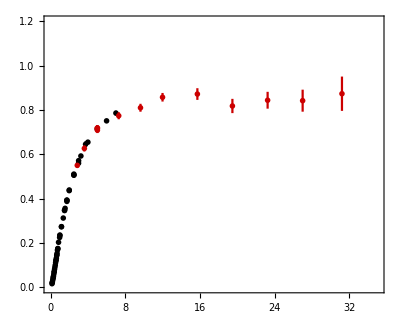

```mathematica
gQ4F1pdata=Show[F1pQ4data,F1pQ4dataSill,Frame->True,PlotRange->{{0,35},{0,1.2}},AspectRatio ->0.8,Axes->False, LabelStyle->Directive[Bold]]
```